```mathematica
?Which
```

```mathematica
boldPlayTail=Function[{x,p,n,a,b}, If[n <0, a+b, Which[0<x≤1/2, boldPlayTail[2*x,p,n-1,a,p*b],1/2<x<1,boldPlayTail[2*x-1,p,n-1,a+p*b,(1-p)*b],x==0,0,x==1,1]]];
boldPlayF=Function[{p,n},Function[{x},boldPlayTail[x,p,n,0,1]]];
boldPlay=Function[{p,n,x},boldPlayF[p,n][x]];
```

```mathematica
boldPlayF[p,1]/@{0,1}
```

{0,1}

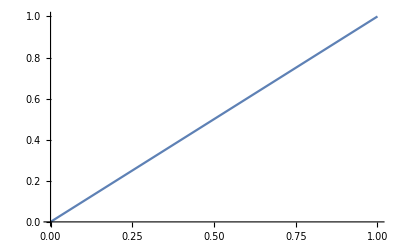

```mathematica
Plot[boldPlay[0.5,32,x],{x,0,1}]
```

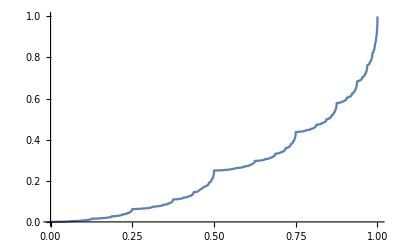

```mathematica
Plot[boldPlay[0.25,32,x],{x,0,1}]
```

```mathematica
Animate[Plot[boldPlay[p,32,x],{x,0,1}],{p,0,1,0.01}]
```

```mathematica
boldPlay[0.5,32,0.9]
```

0.9

```mathematica
(20000-100)/20000
```

199/200

```mathematica
N[%]
```

0.995

```mathematica
100./20000.
```

0.005

```mathematica
boldPlayF[0.5,32]/@{0.9,0.005}
```

{0.9,0.005}

```mathematica
boldPlayF[13./38.,32]/@{0.9,0.005}
```

{0.735157,0.000232594}

```mathematica
(0.735157-2.65614×10^-5)/(2.65614×10^-5)
```

27676.6

```mathematica
(.000232594-2.66641×10^-911)/(2.66641×10^-911)
```

8.72311459978023×10^906

```mathematica
N[1/100!]
```

1.07151×10^-158

```mathematica
?Odds
```

Information::notfound: Symbol Odds not found.